### Density

```mathematica
ClearAll[linspace]
linspace[s_,f_,1]:=(f+s)/2
linspace[s_,f_,n_]:=Range[s,f,(f-s)/(n-1)]
```

```mathematica
Deri[xvec_,h_]:=Join[{1/h(1/5*xvec[[6]]-5/4*xvec[[5]]+10/3*xvec[[4]]-5xvec[[3]]+5xvec[[2]]-137/60xvec[[1]]),1/h(1/5*xvec[[7]]-5/4*xvec[[6]]+10/3*xvec[[5]]-5xvec[[4]]+5xvec[[3]]-137/60xvec[[2]])},Table[1/h(-1/12*xvec[[i+2]]+2/3xvec[[i+1]]-2/3xvec[[i-1]]+1/12xvec[[i-2]]),{i,3,Length[xvec]-2}],{-1/h(1/5*xvec[[Length[xvec]-6]]-5/4*xvec[[Length[xvec]-5]]+10/3*xvec[[Length[xvec]-4]]-5xvec[[Length[xvec]-3]]+5xvec[[Length[xvec]-2]]-137/60xvec[[Length[xvec]-1]]),-1/h(1/5*xvec[[Length[xvec]-5]]-5/4*xvec[[Length[xvec]-4]]+10/3*xvec[[Length[xvec]-3]]-5xvec[[Length[xvec]-2]]+5xvec[[Length[xvec]-1]]-137/60xvec[[Length[xvec]]])}]
```

```mathematica
bcoeff[p_,a_,λ_,n_,c_]:=(p-n)(c+a+λ*(n-p-1))
dcoeff[p_,a_,λ_,n_]:=p(λ(n-p)+a)
```

```mathematica
Clear[LaguerreRecHardv0]
LaguerreRecHardv0[n_,λ_,a_,β_,cpow_,xmin_,xmax_,mesh_]:=Module[{c,RowL,dRowL,Lvec,count,p,h,xvec,xvecS,IC,intRowL,dintRowL},
c=cpow;
SetPrecision[RowL,500];
xvec=linspace[xmin,xmax,mesh];
scale=1/(4(n+1));
xvecS=(xvec*scale);
h=xvecS[[2]]-xvecS[[1]];
IC=(β/2)^(n β)((n+1)*Gamma[1+λ])/(Gamma[1+λ(n+1)]Gamma[c+1+λ*n]);
For[count=1,count≤a,count++,
RowL={};
RowL=If[count==1,Append[RowL,IC*ConstantArray[1,Length[xvec]]],Append[RowL,Lvec]];
For[p=1,p≤n,p++,
(*intRowL=Interpolation[Transpose[{xvecS,Last[RowL]}]];
dintRowL[x_]:=intRowL'[x];
dRowL=Map[dintRowL,xvecS];*)
dRowL=N[Deri[Last[RowL],h],500];
RowL=Append[RowL,((λ(n-p+1)*xvecS+bcoeff[p-1,count,λ,n,c])/(λ(n-p+1)))*Last[RowL]+xvecS/(λ(n-p+1))*dRowL-If[p==1,0,dcoeff[p-1,count,λ,n]/(λ(n-p+1))xvecS*First[Take[RowL,-2]]]]
];
Lvec=Last[RowL];
];
Return[Transpose[{xvec,scale*(xvecS)^(c)*Exp[-xvecS*β/2]*Lvec}]]
];
```

```mathematica
Clear[LaguerreRecHard]
LaguerreRecHard[n_,λ_,a_,β_,cpow_,xmin_,xmax_,mesh_]:=Module[{c,RowL,dRowL,Lvec,count,p,h,xvec,xvecS,IC,intRowL,dintRowL},
c=cpow;
SetPrecision[RowL,500];
xvec=linspace[xmin,xmax,mesh];
scale=1/(4((n+1)+c/β));
xvecS=(xvec*scale);
h=xvecS[[2]]-xvecS[[1]];
IC=(β/2)^(n β)((n+1)*Gamma[1+λ])/(Gamma[1+λ(n+1)]Gamma[c+1+λ*n]);
For[count=1,count≤a,count++,
RowL={};
RowL=If[count==1,Append[RowL,IC*ConstantArray[1,Length[xvec]]],Append[RowL,Lvec]];
For[p=1,p≤n,p++,
(*intRowL=Interpolation[Transpose[{xvecS,Last[RowL]}]];
dintRowL[x_]:=intRowL'[x];
dRowL=Map[dintRowL,xvecS];*)
dRowL=N[Deri[Last[RowL],h],500];
RowL=Append[RowL,((λ(n-p+1)*xvecS+bcoeff[p-1,count,λ,n,c])/(λ(n-p+1)))*Last[RowL]+xvecS/(λ(n-p+1))*dRowL-If[p==1,0,dcoeff[p-1,count,λ,n]/(λ(n-p+1))xvecS*First[Take[RowL,-2]]]]
];
Lvec=Last[RowL];
];
Return[Transpose[{xvec,scale*(xvecS)^(c)*Exp[-xvecS*β/2]*Lvec}]]
];
```

### Plot Checks

```mathematica
(* beta=2 compared against known limiting density *)
Show[ListPlot[LaguerreRecHard[50,1,2,2,1,0,100,10000],PlotRange->{0,0.075}],Plot[1/4(BesselJ[1,Sqrt[x]]^2-BesselJ[2,Sqrt[x]]*BesselJ[0,Sqrt[x]]),{x,0,100},PlotStyle->{Red,Dashed}]]
```

-Graphics-

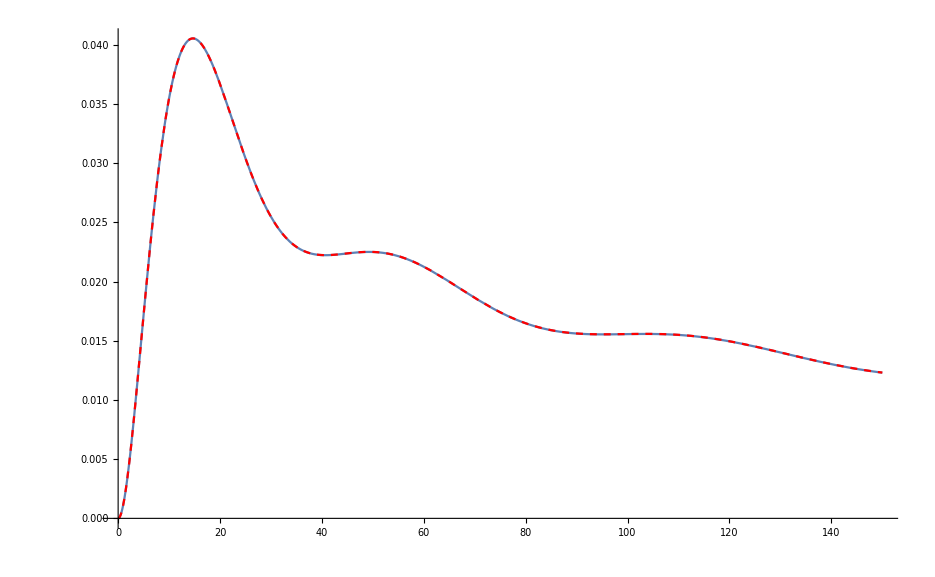

```mathematica
Show[Plot[FixedInf100β2[x],{x,0,150}],Plot[1/4(BesselJ[2,Sqrt[x]]^2-BesselJ[3,Sqrt[x]]*BesselJ[1,Sqrt[x]]),{x,0,150},PlotStyle->{Red,Dashed}]]
```

```mathematica
FixedInf100β2=Interpolation[LaguerreRecHard[99,1,2,2,2,0,200,2000]];
FixedInf100β2v0=Interpolation[LaguerreRecHardv0[99,1,2,2,2,0,200,2000]];
```

```mathematica
FixedInfLarge=Interpolation[LaguerreRecHard[10000,1,2,2,2,0,200,1000]];
```

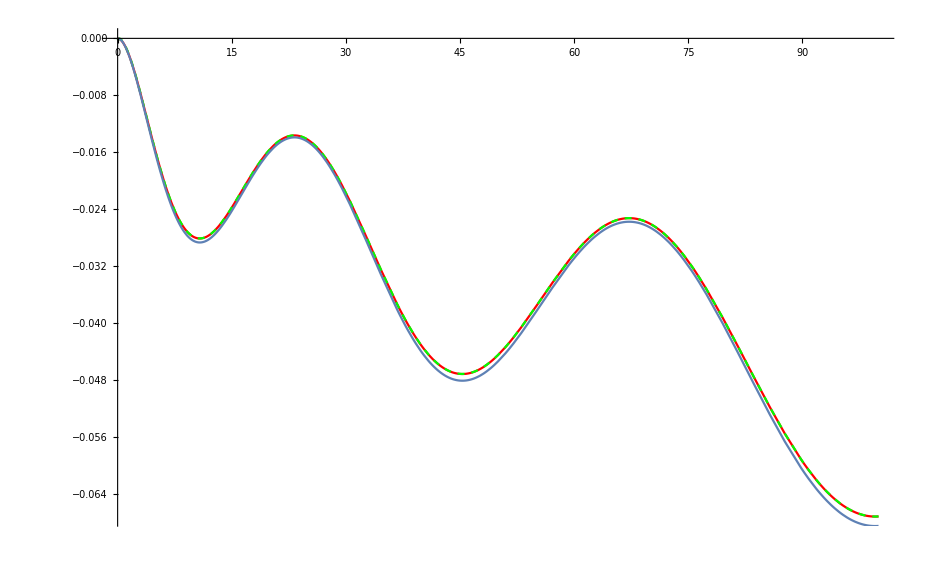

```mathematica
Show[Plot[100^2(FixedInf100β2[x]-1/4(BesselJ[2,Sqrt[x]]^2-BesselJ[3,Sqrt[x]]*BesselJ[1,Sqrt[x]])),{x,0,100},PlotStyle->Red],Plot[100^2(FixedInf100β2[x]-FixedInfLarge[x]),{x,0,100},PlotStyle->{Dashed,Green}],Plot[-1/192((2x+4)BesselJ[2,Sqrt[x]]^2+4Sqrt[x]BesselJ[2,Sqrt[x]](D[BesselJ[2,t],t]/.t->Sqrt[x])+x(D[BesselJ[2,t],t]/.t->Sqrt[x])^2),{x,0,100}]]
```

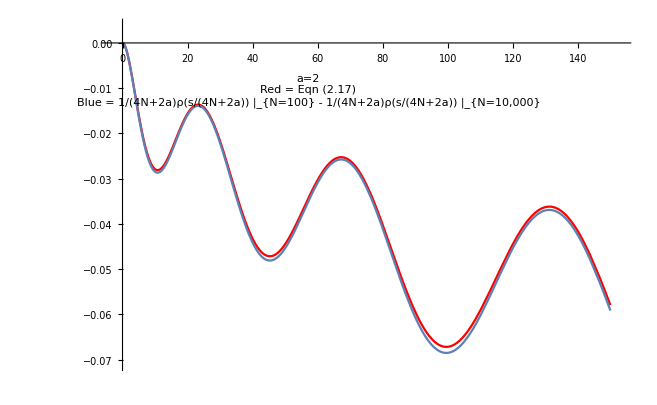

```mathematica
FixedInf100β2a3=Interpolation[LaguerreRecHard[99,1,2,2,3,0,200,1000]];
FixedInf100β2a3v0=Interpolation[LaguerreRecHardv0[99,1,2,2,3,0,200,1000]];
```

```mathematica
FixedInfLargea3=Interpolation[LaguerreRecHard[10000,1,2,2,3,0,200,1000]];
```

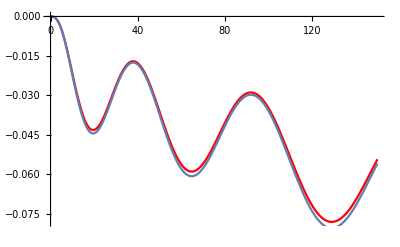

```mathematica
Show[Plot[100^2(FixedInf100β2a3[x]-FixedInfLargea3[x]),{x,0,150},PlotStyle->Red],Plot[-1/192((2x+9)BesselJ[3,Sqrt[x]]^2+4Sqrt[x]BesselJ[3,Sqrt[x]](D[BesselJ[3,t],t]/.t->Sqrt[x])+x(D[BesselJ[3,t],t]/.t->Sqrt[x])^2),{x,0,150}]]
```

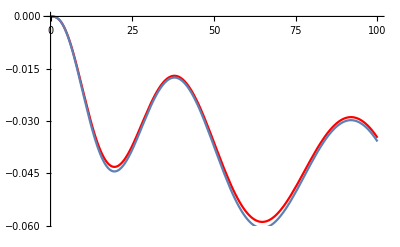

```mathematica
Show[Plot[100^2(FixedInf100β2a3[x]-FixedInfLargea3[x]),{x,0,100},PlotStyle->Red],Plot[-1/192((2x+9)BesselJ[3,Sqrt[x]]^2+4Sqrt[x]BesselJ[3,Sqrt[x]](D[BesselJ[3,t],t]/.t->Sqrt[x])+x(D[BesselJ[3,t],t]/.t->Sqrt[x])^2),{x,0,100}]]
```

### Plots

```mathematica
FixedInf50β4a2=Interpolation[LaguerreRecHard[49,2,4,4,2,0,200,100]];
FixedInf50β4a2v0=Interpolation[LaguerreRecHardv0[49,2,4,4,2,0,200,100]];
```

```mathematica
FixedInf100β4a2=Interpolation[LaguerreRecHard[99,2,4,4,2,0,200,100]];
FixedInf100β4a2v0=Interpolation[LaguerreRecHardv0[99,2,4,4,2,0,200,100]];
```

```mathematica
FixedInfLargeβ4a2=Interpolation[LaguerreRecHard[10000,2,4,4,2,0,200,100]];
```

```mathematica
FixedInf50a2=Interpolation[LaguerreRecHard[49,3,6,6,2,0,200,100]];
FixedInf50a2v0=Interpolation[LaguerreRecHardv0[49,3,6,6,2,0,200,100]];
```

```mathematica
FixedInf100a2=Interpolation[LaguerreRecHard[99,3,6,6,2,0,200,100]];
FixedInf100a2v0=Interpolation[LaguerreRecHardv0[99,3,6,6,2,0,200,100]];
```

```mathematica
FixedInfLargea2=Interpolation[LaguerreRecHard[10000,3,6,6,2,0,200,100]];
```

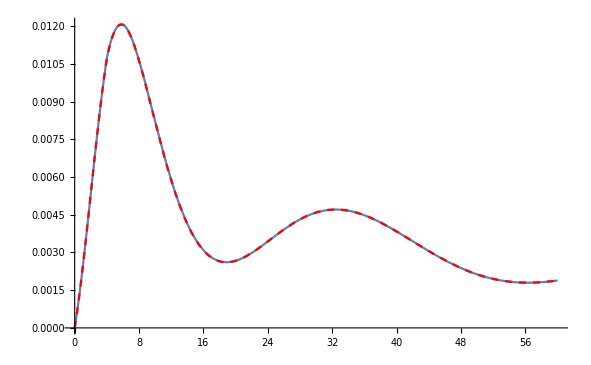

```mathematica
Show[Plot[(FixedInf50β4a2[x]),{x,0,60},PlotRange->Full],Plot[FixedInfLargeβ4a2[x],{x,0,60},PlotStyle->{Red,Dashed},PlotRange->Full]]
```

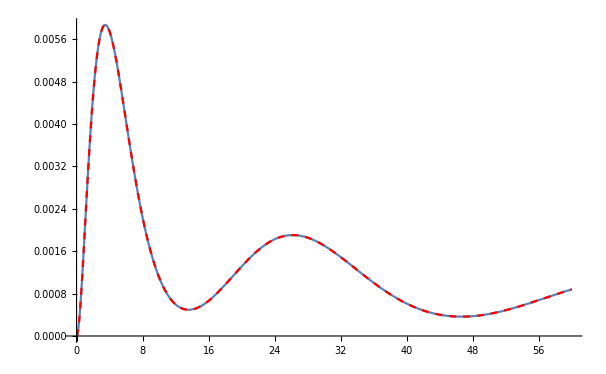

```mathematica
Show[Plot[(FixedInf50a2[x]),{x,0,60},PlotRange->Full],Plot[FixedInfLargea2[x],{x,0,60},PlotStyle->{Red,Dashed},PlotRange->Full]]
```

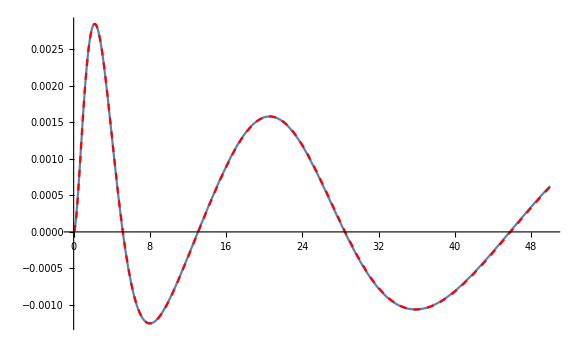

```mathematica
Show[Plot[Evaluate[100*(FixedInf50a2v0[x]-FixedInf50a2[x]),{x,0,50}]],Plot[Evaluate[2/6*(x*FixedInfLargea2'[x]+FixedInfLargea2[x]),{x,0,50}],PlotStyle->{Red,Dashed}]]
```

```mathematica
(* beta =4, N-100 *)
Show[Plot[50^2(FixedInf50β4a2[x]-FixedInfLargeβ4a2[x]),{x,0,120}],Plot[100^2(FixedInf100β4a2[x]-FixedInfLargeβ4a2[x]),{x,0,120},PlotStyle->{Red,Dashed}]]
```

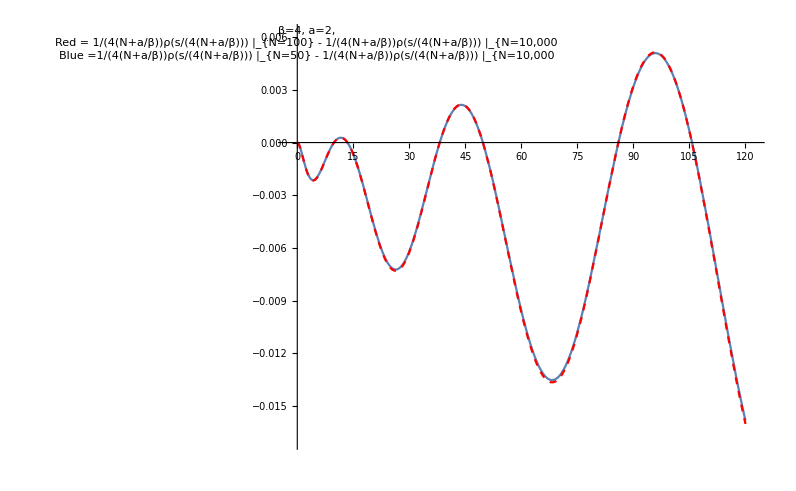

```mathematica
(* beta =6, N-100 *)
Show[Plot[50^2(FixedInf50a2[x]-FixedInfLargea2[x]),{x,0,120}],Plot[50^2(FixedInf50a2[x]-FixedInfLargea2[x]),{x,0,120},PlotStyle->{Red,Dashed}]]
```

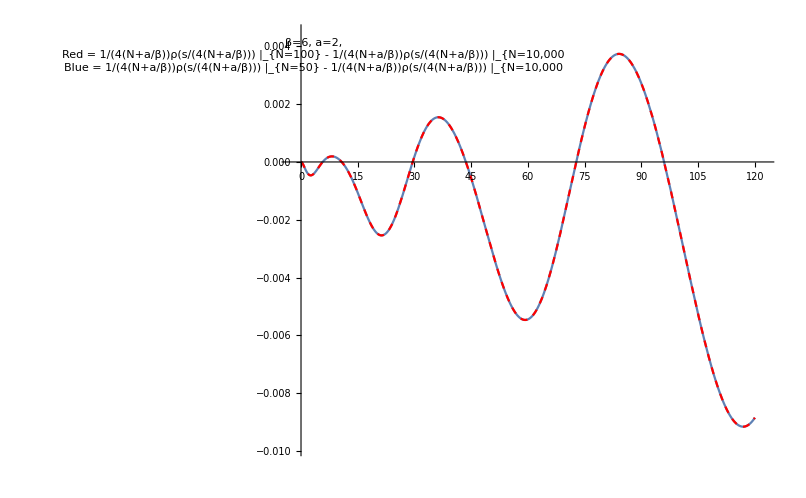

```mathematica
FixedInf50a3=Interpolation[LaguerreRecHard[49,3,6,6,3,0,200,500]];
FixedInf50a3v0=Interpolation[LaguerreRecHardv0[49,3,6,6,3,0,200,500]];
```

```mathematica
FixedInf100a3=Interpolation[LaguerreRecHard[99,3,6,6,3,0,200,500]];
FixedInf100a3v0=Interpolation[LaguerreRecHardv0[99,3,6,6,3,0,200,500]];
```

```mathematica
FixedInfLargea3=Interpolation[LaguerreRecHard[10000,3,6,6,3,0,200,500]];
```

```mathematica
Show[Plot[50^2(FixedInf50a3[x]-FixedInfLargea3[x]),{x,0,80},AxesLabel->{Style["s",Bold,16]},TicksStyle->Directive[Bold, 20],GridLines->Automatic],Plot[50^2(FixedInf50a3[x]-FixedInfLargea3[x]),{x,0,80},PlotStyle->{Red,Dashed}]]
```

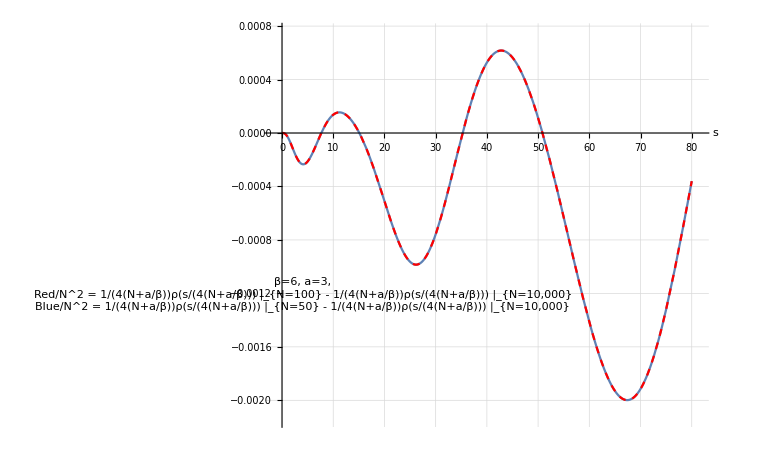

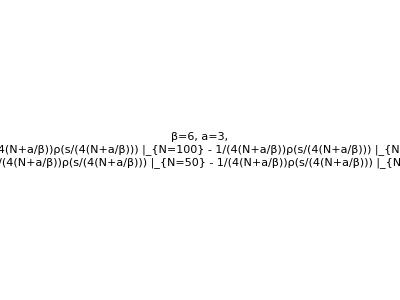

```mathematica
(* beta =6, N-100 *)
Show[Plot[50^2(FixedInf50a3[x]-FixedInfLargea3[x]),{x,0,120}],Plot[50^2(FixedInf50a3[x]-FixedInfLargea3[x]),{x,0,120},PlotStyle->{Red,Dashed}]]
```

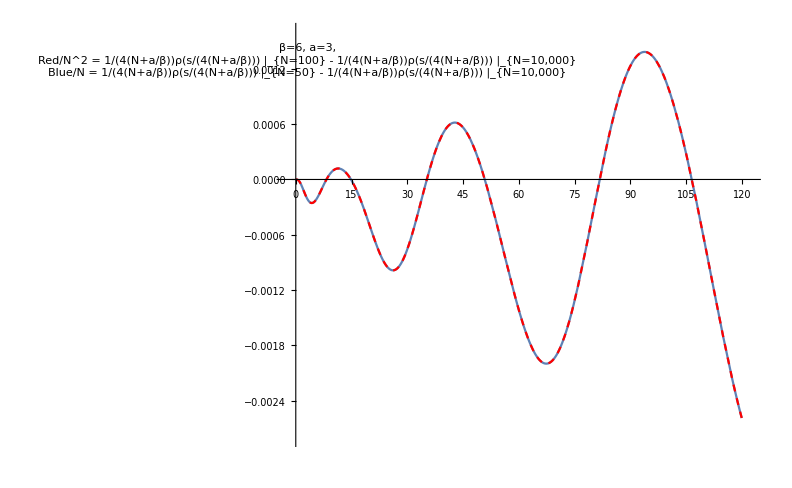

### Gap probability

```mathematica
bcoeff[p_,a_,λ_,n_,c_]:=(p-n)(c+a+λ*(n-p-1))
dcoeff[p_,a_,λ_,n_]:=p(λ(n-p)+a)
```

```mathematica
Clear[GapLaguerreRecHardv0]
GapLaguerreRecHardv0[n_,β_,cpow_,s_,mesh_]:=Module[{RowL,dRowL,Lvec,count,p,h,xvec,svec,xvecS,IC,intRowL,dintRowL,w},
SetPrecision[RowL,500];
xvec=linspace[-s,0,mesh];
svec=linspace[0,s,mesh];
xvecS=xvec/(4(n));
h=xvecS[[2]]-xvecS[[1]];
IC=(β/2)^(cpow*(n))/(Product[Pochhammer[1+(j-1)β/2,cpow],{j,1,n}]);
For[count=1,count≤cpow,count++,
RowL={};
RowL=If[count==1,Append[RowL,IC*ConstantArray[1,Length[xvec]]],Append[RowL,Lvec]];
For[p=1,p≤n,p++,
(*intRowL=Interpolation[Transpose[{xvecS,Last[RowL]}]];
dintRowL[x_]:=intRowL'[x];
dRowL=Map[dintRowL,xvecS];*)
dRowL=N[Deri[Last[RowL],h],500];
RowL=Append[RowL,((β/2*(n-p+1)*xvecS+bcoeff[p-1,count,β/2,n,0])/(β/2*(n-p+1)))*Last[RowL]+xvecS/(β/2*(n-p+1))*dRowL-If[p==1,0,dcoeff[p-1,count,β/2,n]/(β/2*(n-p+1))xvecS*First[Take[RowL,-2]]]]
];
Lvec=Last[RowL];
];
Return[Transpose[{svec,Exp[-β*n/2*svec/(4(n))]*Reverse[Lvec]}]]
];
GapLaguerreRecHard[n_,β_,cpow_,s_,mesh_]:=Module[{RowL,dRowL,Lvec,count,p,h,xvec,svec,xvecS,IC,intRowL,dintRowL,w},
SetPrecision[RowL,500];
xvec=linspace[-s,0,mesh];
svec=linspace[0,s,mesh];
xvecS=xvec/(4(n+cpow/β));
h=xvecS[[2]]-xvecS[[1]];
IC=(β/2)^(cpow*(n))/(Product[Pochhammer[1+(j-1)β/2,cpow],{j,1,n}]);
For[count=1,count≤cpow,count++,
RowL={};
RowL=If[count==1,Append[RowL,IC*ConstantArray[1,Length[xvec]]],Append[RowL,Lvec]];
For[p=1,p≤n,p++,
(*intRowL=Interpolation[Transpose[{xvecS,Last[RowL]}]];
dintRowL[x_]:=intRowL'[x];
dRowL=Map[dintRowL,xvecS];*)
dRowL=N[Deri[Last[RowL],h],500];
RowL=Append[RowL,((β/2*(n-p+1)*xvecS+bcoeff[p-1,count,β/2,n,0])/(β/2*(n-p+1)))*Last[RowL]+xvecS/(β/2*(n-p+1))*dRowL-If[p==1,0,dcoeff[p-1,count,β/2,n]/(β/2*(n-p+1))xvecS*First[Take[RowL,-2]]]]
];
Lvec=Last[RowL];
];
Return[Transpose[{svec,Exp[-β*n/2*svec/(4(n+cpow/β))]*Reverse[Lvec]}]]
];
```

### Plot checks

```mathematica
GapFixedInfbeta2v0=Interpolation[GapLaguerreRecHardv0[30,2,2,100,500]];
GapFixedInfbeta2=Interpolation[GapLaguerreRecHard[30,2,2,100,500]];
```

```mathematica
GapFixedInfLargebeta2a2=Interpolation[GapLaguerreRecHard[10000,2,2,100,500]];
```

```mathematica
M[x_,a_]:=Table[BesselI[Abs[i-j],x],{i,a},{j,a}]
m[x_,a_]:=Table[BesselI[Abs[2+i-j],x],{i,a},{j,a}]
m1[x_,a_]:=Table[BesselI[Abs[4+i-j],x],{i,a},{j,a}]
Finf[x_,a_]:=Exp[-x/4]*Det[M[Sqrt[x],a]]
finf[x_,a_]:=1/2 Exp[-x/4]*Det[m[Sqrt[x],a]]
f1inf1[x_,a_]:=1/4 Exp[-x/4]*Det[m1[Sqrt[x],a]]
```

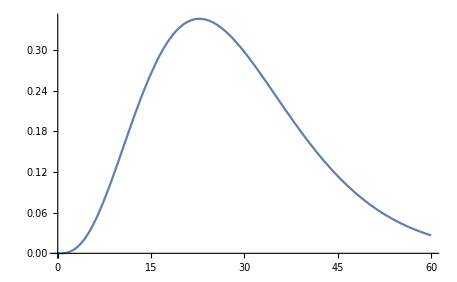

```mathematica
Plot[30^2(GapFixedInfbeta2[x]-Finf[x,2]),{x,0,60}]
```

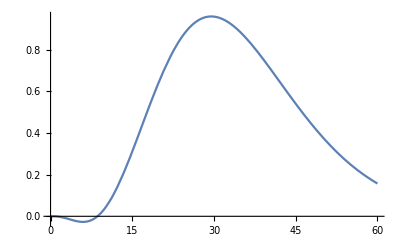

```mathematica
Plot[30^2(GapFixedInfbeta2v0[x]-GapFixedInfLargebeta2a2[x]-x/30 GapFixedInfLargebeta2a2'[x]),{x,0,60}]
```

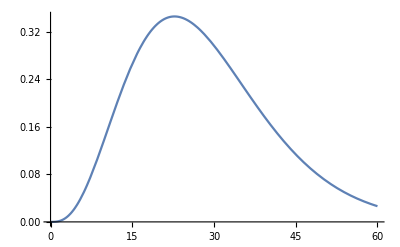

```mathematica
Plot[30^2(GapFixedInfbeta2[x]-GapFixedInfLargebeta2a2[x]),{x,0,60}]
```

### Plots

```mathematica
GapFixedInf50a2v0=Interpolation[GapLaguerreRecHardv0[50,6,2,50,500]];
GapFixedInf50a2=Interpolation[GapLaguerreRecHard[50,6,2,50,500]];
```

```mathematica
GapFixedInf100a2v0=Interpolation[GapLaguerreRecHardv0[100,6,2,50,500]];
GapFixedInf100a2=Interpolation[GapLaguerreRecHard[100,6,2,50,500]];
```

```mathematica
GapFixedInfLargea2=Interpolation[GapLaguerreRecHard[10000,6,2,50,500]];
```

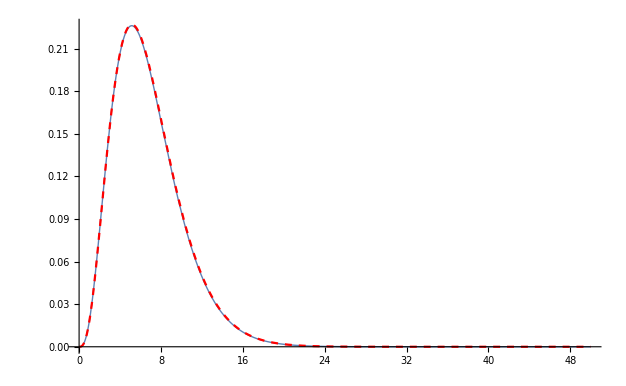

```mathematica
Show[Plot[Evaluate[(50)*(GapFixedInf50a2[x]-GapFixedInf50a2v0[x]),{x,0,50},PlotStyle->{Thick}]],Plot[Evaluate[-2/6*(x*GapFixedInfLargea2'[x]),{x,0,50}],PlotStyle->{Red,Dashed}]]
```

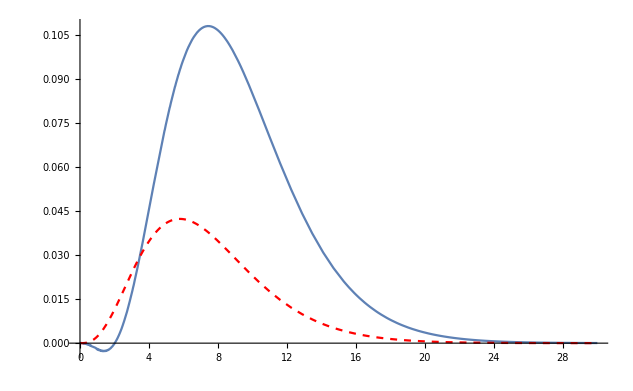

```mathematica
Show[Plot[50^2(GapFixedInf50a2v0[x]-GapFixedInfLargea2[x]-2/(6*50)x D[GapFixedInfLargea2[s],s]/.s->x),{x,0,30}],Plot[100^2(GapFixedInf100a2[x]-GapFixedInfLargea2[x]),{x,0,30},PlotStyle->{Red,Dashed}]]
```

```mathematica
Show[Plot[50^2(GapFixedInf50a2[x]-GapFixedInfLargea2[x]),{x,0,30},PlotStyle->{Bold,Thick}],Plot[100^2(GapFixedInf100a2[x]-GapFixedInfLargea2[x]),{x,0,30},PlotStyle->{Red,Dashed}]]
```

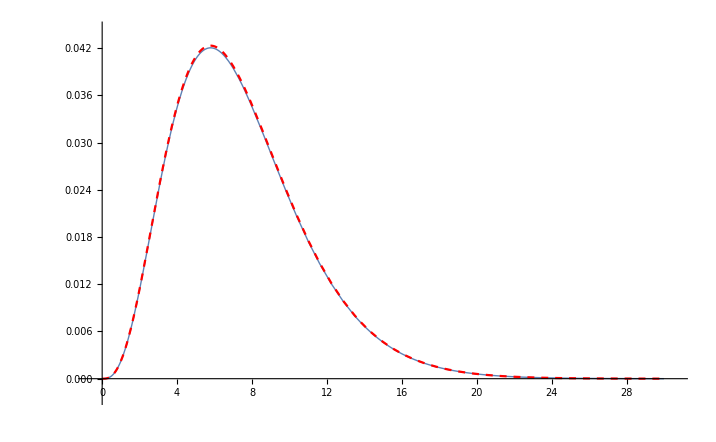

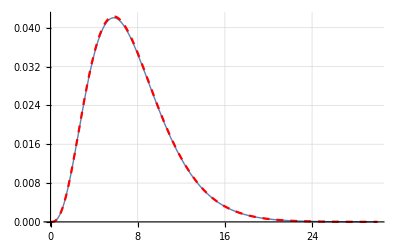
-Graphics-N^2[E_(N, β)(s)-E_(∞, β)(s)]s

```mathematica
Labeled[
Show[-Graphics-,
PlotRange->All,LabelStyle->Directive[FontSize->12],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],ImageSize->{1000},TicksStyle->Directive[Black, 20]],
{"N^2[E_(N, β)(s)-E_(∞, β)(s)]","s"},{Left,Bottom},RotateLabel->True,LabelStyle->Directive[Bold, 20]]
```

```mathematica
GapFixedInfLargea1=Interpolation[GapLaguerreRecHard[10000,6,1,50,500]];
```

```mathematica
GapFixedInf50a1=Interpolation[GapLaguerreRecHard[50,6,1,50,500]];
GapFixedInf50a1v0=Interpolation[GapLaguerreRecHardv0[50,6,1,50,500]];
```

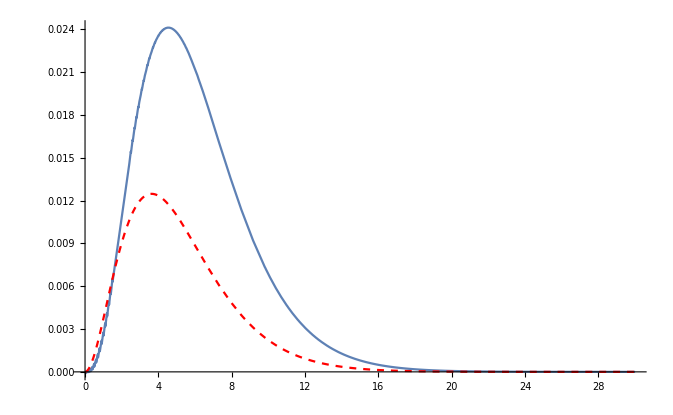

```mathematica
Show[Plot[50^2(GapFixedInf50a1v0[x]-GapFixedInfLargea1[x]-1/(6*50)x D[GapFixedInfLargea1[s],s]/.s->x),{x,0,30}],Plot[s/48*Exp[-β s/8]((-1+1/β) Hypergeometric0F1[2/β,s/4]+((1-1/β)+s β/8 )Hypergeometric0F1[2/β+1,s/4])/.β->6,{s,0,30},PlotStyle->{Red,Dashed}]]
```

```mathematica
GapFixedInf50a1=Interpolation[GapLaguerreRecHard[50,6,1,50,500]];
Show[Plot[50^2(GapFixedInf50a1[x]-GapFixedInfLargea1[x]),{x,0,30}],Plot[s/48*Exp[-β s/8]((-1+1/β) Hypergeometric0F1[2/β,s/4]+((1-1/β)+s β/8 )Hypergeometric0F1[2/β+1,s/4])/.β->6,{s,0,30},PlotStyle->{Red,Dashed}]]
```

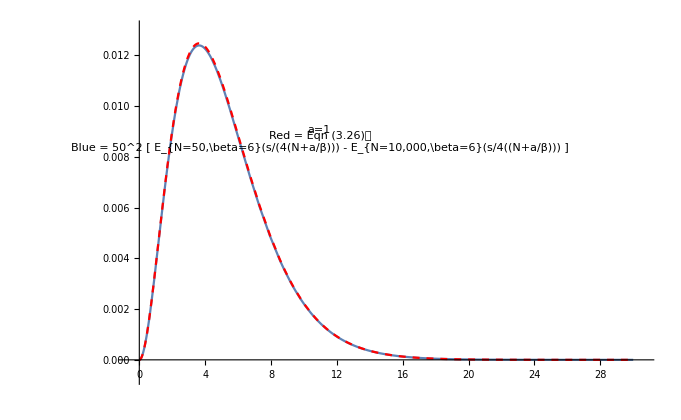

```mathematica
GapFixedInf50a2v0=Interpolation[GapLaguerreRecHardv0[50,6,2,50,500]];
GapFixedInf50a2=Interpolation[GapLaguerreRecHard[50,6,2,50,500]];
```

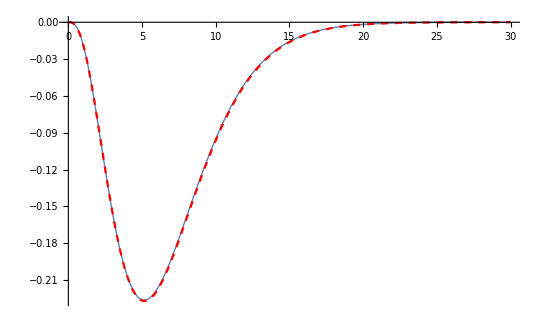

```mathematica
Show[Plot[Evaluate[(50)*(GapFixedInf50a2v0[x]-GapFixedInf50a2[x]),{x,0,30},PlotStyle->{Thick}]],Plot[Evaluate[2/6*(x*GapFixedInfLargea2'[x]),{x,0,30}],PlotStyle->{Red,Dashed}]]
```

```mathematica
GapFixedInf50a3v0=Interpolation[GapLaguerreRecHardv0[50,6,3,50,500]];
GapFixedInf50a3=Interpolation[GapLaguerreRecHard[50,6,3,50,500]];
```

```mathematica
GapFixedInf100a3v0=Interpolation[GapLaguerreRecHardv0[100,6,3,50,500]];
GapFixedInf100a3=Interpolation[GapLaguerreRecHard[100,6,3,50,500]];
```

```mathematica
GapFixedInfLargea3=Interpolation[GapLaguerreRecHard[10000,6,3,50,500]];
```

```mathematica
Show[Plot[50^2(GapFixedInf50a3[x]-GapFixedInfLargea3[x]),{x,0,30}],Plot[100^2(GapFixedInf100a3[x]-GapFixedInfLargea3[x]),{x,0,30},PlotStyle->{Red,Dashed}]]
```